```mathematica
Clear["@"];
```

Clear::wrsym: Symbol a is Protected.

Clear::wrsym: Symbol b is Protected.

Clear::wrsym: Symbol c is Protected.

General::stop: Further output of Clear :: wrsym will be suppressed during this calculation.

```mathematica
<<ICA`;
<<PCA`;
<<matcher`;
<<classifier`;
<<Data`;
```

```mathematica
data=nxrData[-1];
Dimensions[data]
```

{50,2,6,46}

# Use Arch II, that is, use each feature(like freq) as signal, each measure as sample

in this way, what we get are independent and compact new features

## First use all data

```mathematica
fft=Flatten[data,{{1,2},{3,4}}];
Dimensions[fft]
```

{100,276}

### first use PCA to reduce dim

```mathematica
{tm,l,p}=mPCA[fft];
tp=p[[All,;;99]];
Dimensions[tp]
```

{100,99}

```mathematica
Chop[tm.tmᵀ][[;;10]];
Max[Chop[p-fft.tmᵀ]]
```

```mathematica
(*the pca sample we use:*)
```

```mathematica
ppc=Partition[tp,2];
Dimensions[%]
```

{50,2,99}

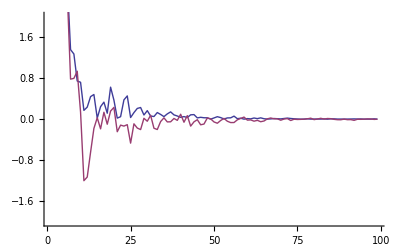
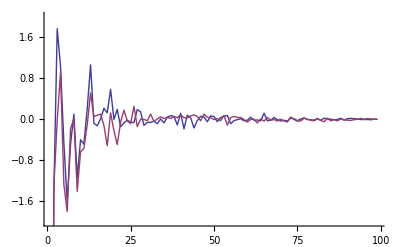
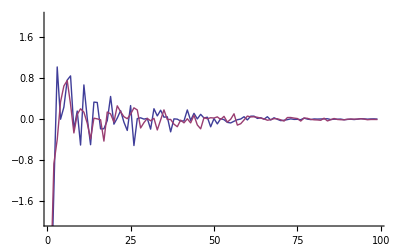
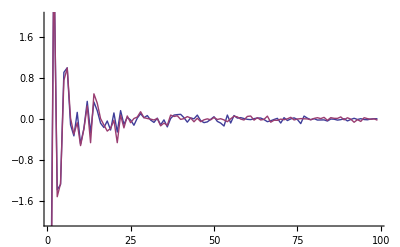
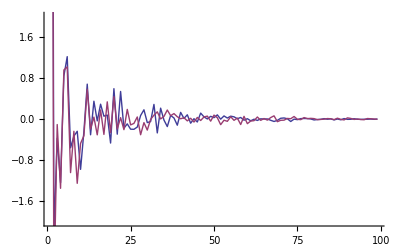
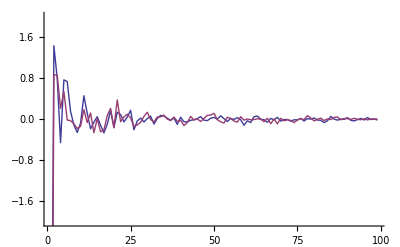
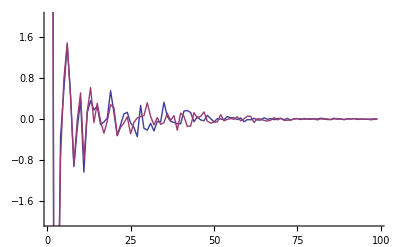
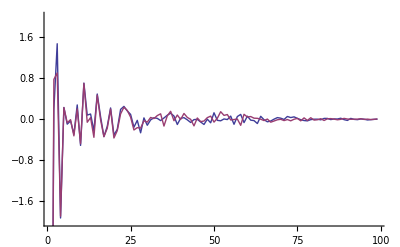

```mathematica
Table[ListPlot[ppc[[i]],Joined->True,PlotRange->{-2,2}],{i,10}]
(*first several PCs work*)
```

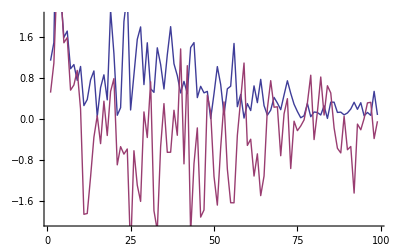
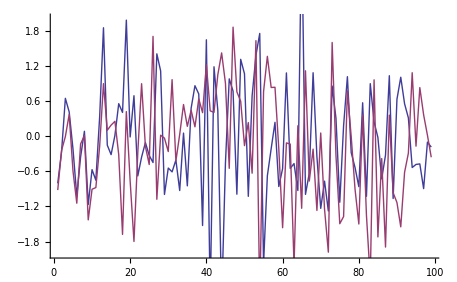
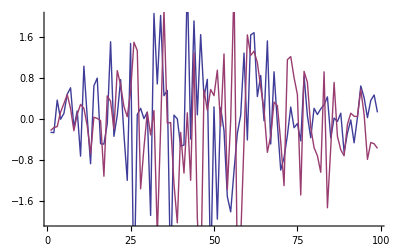
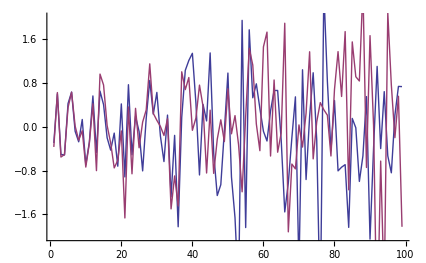
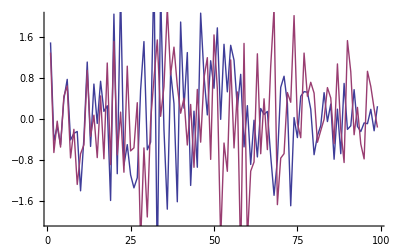
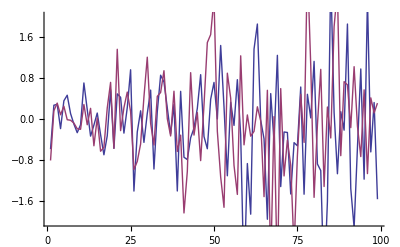
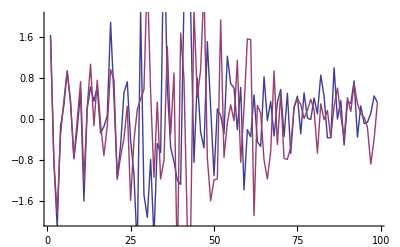
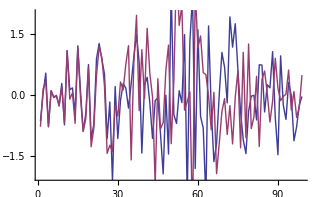

```mathematica
(* what if we standzrdize pcs*)
spc=Standardize[tp];
Table[ListPlot[Partition[spc,2][[i]],Joined->True,PlotRange->{-2,2}],{i,10}]
(* the inner class diff is amplified,so not standardize*)
```

```mathematica
(*ScatterPlot[ppc[[;;50,;;,;;5]],{{-10,10},{-10,10}}]*)
```

```mathematica
{dd,ds}=eucDistV[ppc];
Dimensions[dd]
```

{4900,99}

```mathematica
ddis={dd[[;;200,;;5]],ds[[;;,;;5]]};
(*Dimensions[ddis[[2]]]*)
```

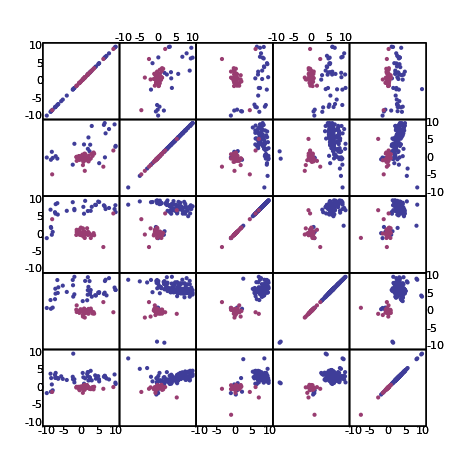

```mathematica
ScatterPlot[ddis,{{-10,10},{-10,10}}]
```

### now ICA using PCs (but should not use all data of same person)

```mathematica
tp1=ppc[[All,1]];
{ic,W,A}=fastICA[tp1ᵀ,retW->True];
```

use deltaW:1/1000, Maxstep:100

Dimension adjusted to 49 according to covariance matrix

Sum of 50 removed eigenvalues(Choped) 0

100.% of (non-zero) eigenvalues retained

Smallest remaining (non-zero) eigenvalue 0.000728528

Largest remaining (non-zero) eigenvalue 243.199

whiten OK

guess OK

total time:0.765625seconds

```mathematica
Dimensions[ic]
Max[Chop[Correlation[icᵀ]]-IdentityMatrix[Length[ic]]]
Dimensions[W]
Chop[ic.icᵀ];
```

{49,50}

6.66134×10^-16

{49,99}

```mathematica
tp2=ppc[[All,2]];
tp2=Standardize[tp2ᵀ,Mean]ᵀ;(*center rows*)
```

```mathematica
ic2=W.tp2ᵀ;
Dimensions[ic2]
Max[Chop[Correlation[ic2ᵀ]]-IdentityMatrix[Length[ic2]]]
(*tic=Partition[icᵀ,2];
Dimensions[tic]*)
```

{49,50}

0.843668

```mathematica
tic={icᵀ,ic2ᵀ}ᵀ;
Dimensions[tic]
```

{50,2,49}

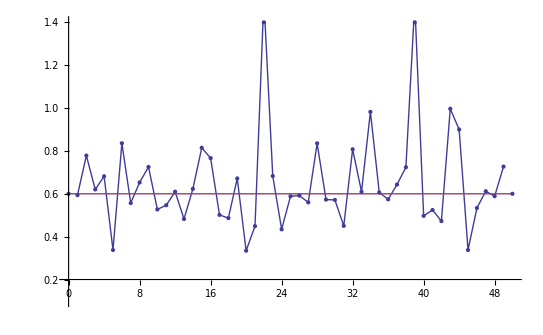

```mathematica
sj1=Table[J1[tic[[;;,;;,i]]],{i,Length[tic[[1,1]]]}];
ListPlot[{sj1,{{0,0.6},{50,0.6}}},Joined->True,PlotRange->{0.1,1.4},Mesh->Full]
```

J1 is not very big for all ICs, so try find first several numbers.

```mathematica
Mean[sj1]
```

0.653422

```mathematica
Select[sj1,#>0.55&]
```

{0.580545,0.931256,0.856053,1.23748,0.618857,0.635704,0.56994,0.560365,0.562202,0.750023,0.570219,0.621207,0.607681,0.550691,0.554537,0.598507,0.58106,0.572972,0.831198,0.71105,0.666046,0.553774,0.676301}

```mathematica
or=Reverse[Ordering[sj1]]
```

{22,39,43,34,44,6,28,15,32,2,16,49,9,38,23,4,19,8,37,14,3,47,12,33,35,1,26,48,25,36,29,30,27,7,11,46,10,41,17,40,18,13,42,31,21,24,5,45,20}

```mathematica
is=tic[[All,All,or[[{1,2}]]]];
Dimensions[is]
{dd,ds}=eucDist[is];
Min[dd]
Max[ds]
{dd1,ds1}=dDist[is,CosineDistance];
Min[dd1]
Max[ds1]
```

{50,2,2}

4.74229×10^-9

7.26563

2.40374×10^-12

1.90504

```mathematica
(*DistList[data_,range_]:=Module[{dd,distx,pdist},
(*generate distribution list for plot,
range is {minx,maxx,dx}*)

dd=Map[BinCounts[#,range]/Length[#]&,data];
distx=Table[i*range[[3]],{i,0,Length[dd[[1]]]-1}];
pdist=Map[Transpose[{distx,#}]&,dd]
];*)
```

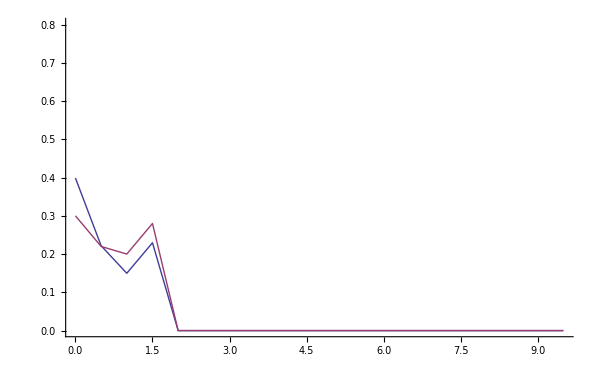

```mathematica
pld=DistList[{dd1,ds1},{0,10,0.5}];
ListPlot[pld,Joined->True,PlotRange->{0,0.8}]
```

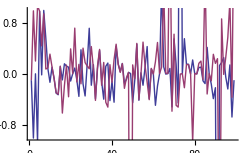
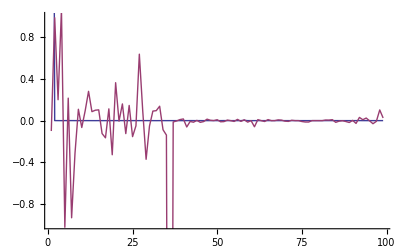
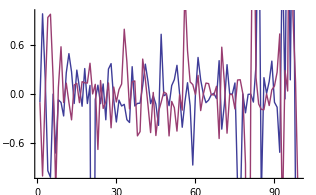
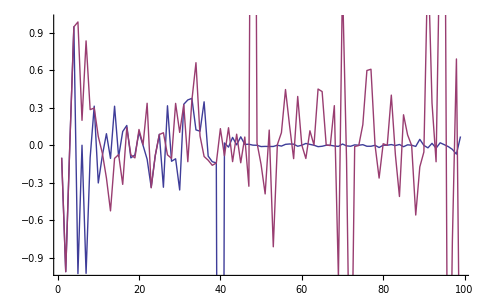
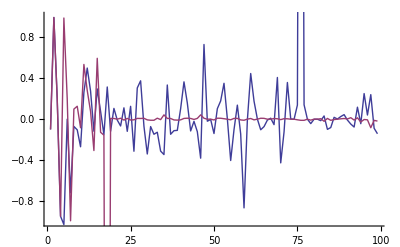
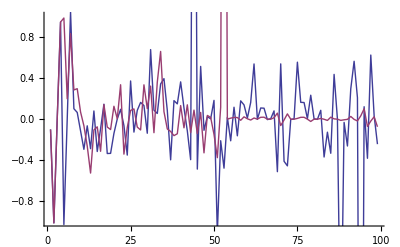
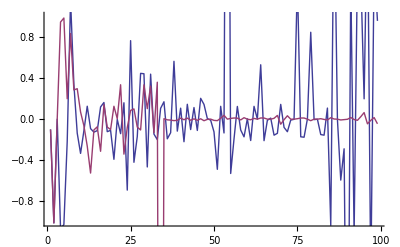
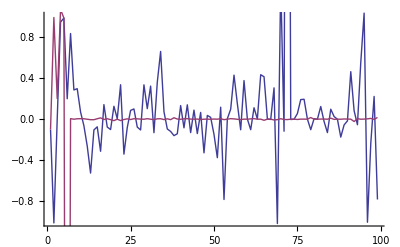

```mathematica
Table[ListPlot[tic[[i]],Joined->True,PlotRange->{-1,1}],{i,10}]
```

```mathematica
templ=is[[All,1]];
pdata=is[[All,2]];
tg=ConstantArray[ConstantArray[0,Length[templ]],Length[pdata]];
For[i=1;k=1;n=1,i≤Length[pdata],i++,
For[m=1,m≤1,m++,
tg[[n,k]]=1;
n++;
];
k++;
];
```

```mathematica
tg//MatrixForm;
```

```mathematica
(* it does not work well...*)
```

```mathematica
EER[pdata,templ,tg,classifyDist1,{0,10,0.005}]
```

{0.675,{0.492653,0.48}}

```mathematica
{dd,ds}=eucDist[is];
```

```mathematica
Mean[dd]
Mean[ds]
```

1.39672

1.26458

```mathematica
TTest[{dd,ds},0,{"TestDataTable","TestConclusion"}]
```

TTest::nortst: At least one of the p-values in {0., 0.}, resulting from a test for normality, is below 0.025. The tests in {"T"} require that the data is normally distributed.

Intersection::normal: Nonatomic expression expected at position 2 in {"PairedT", "T", "Z", "KSampleT"} ∩ "T".

TTest::nortst: At least one of the p-values in {0., 0.}, resulting from a test for normality, is below 0.025. The tests in {"PairedT", "T", "Z", "KSampleT"} ∩ "T" require that the data is normally distributed.

General::stop: Further output of TTest :: nortst will be suppressed during this calculation.

{ | Statistic | P-Value
T | 0.325176 | 0.745061,The null hypothesis that the median difference is 0 is not rejected at the 5. percent level based on the T test.}

### 1 try plot Cs:

```mathematica
Dimensions[tp]
```

{100,99}

```mathematica
stp=Standardize[tp];
sstp=Partition[stp,2];
Dimensions[sstp]
```

{50,2,99}

```mathematica
(*THIS IS std PCs*)
```

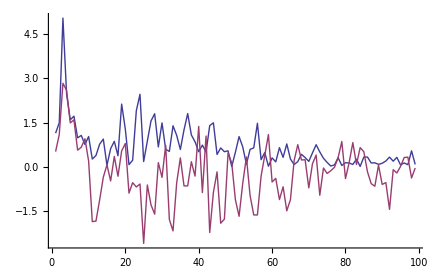
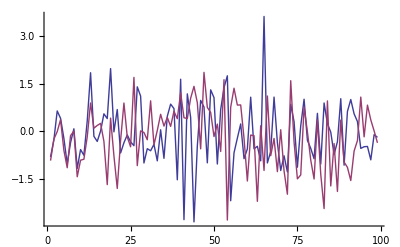
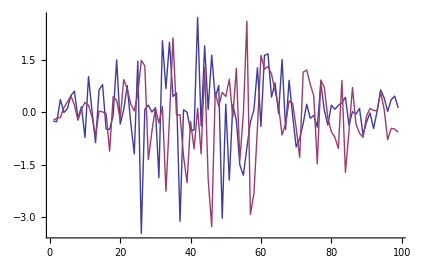
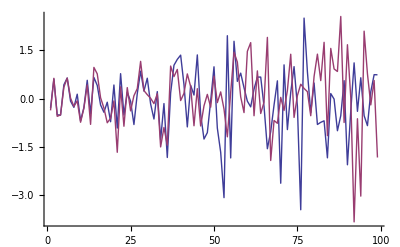
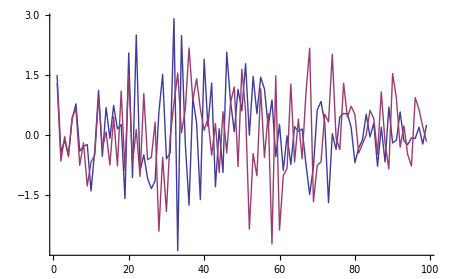
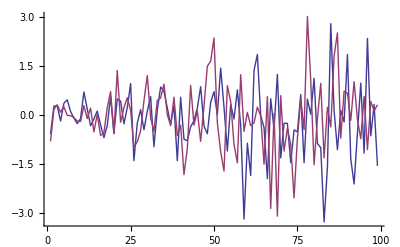
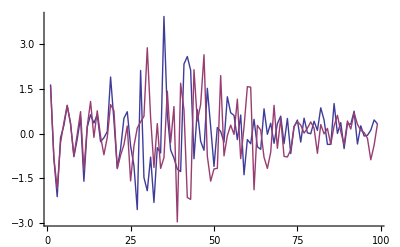
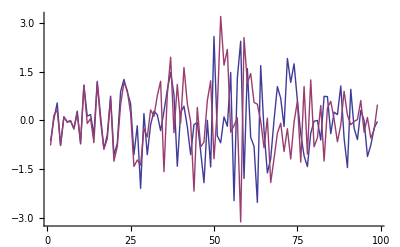

```mathematica
Table[ListPlot[sstp[[i]],Joined->True],{i,10}]
```

```mathematica
(* THIS IS ICs*)
```

The sign, it is important here!!!, Maybe only one measure of a person should be used.

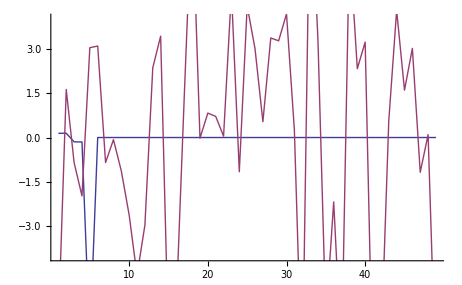
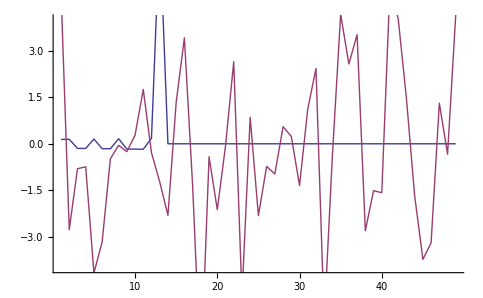
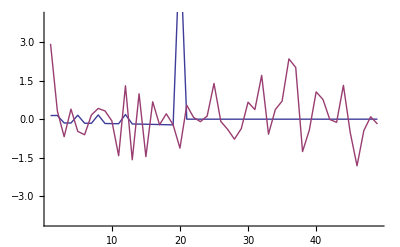
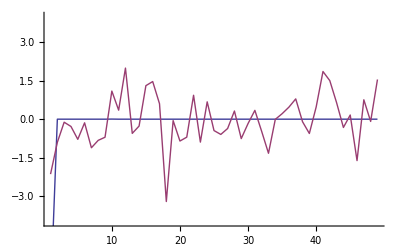
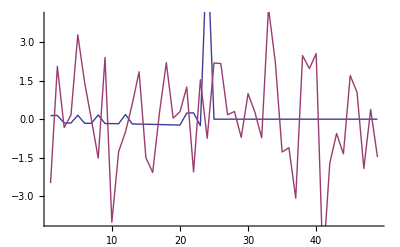
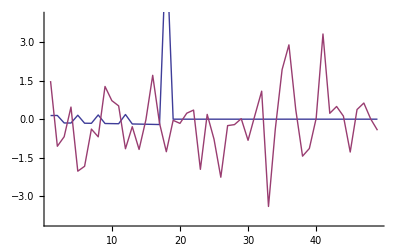
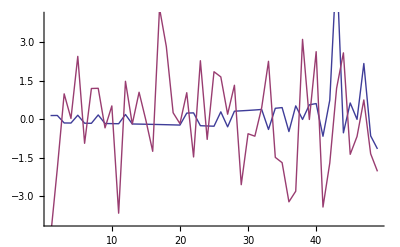
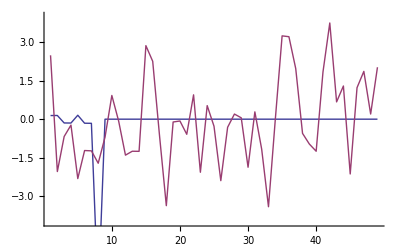

```mathematica
Table[ListPlot[tic[[i]],Joined->True,PlotRange->{-4,4}],{i,10}]
```

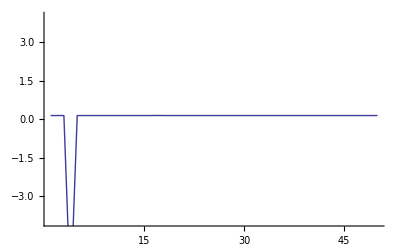
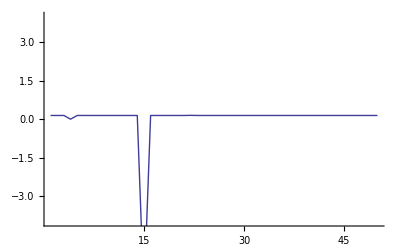
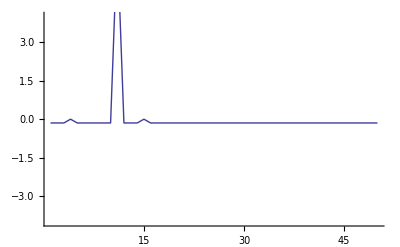
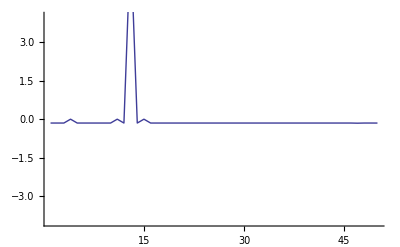
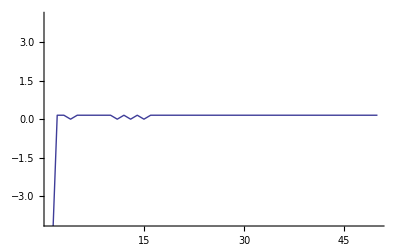
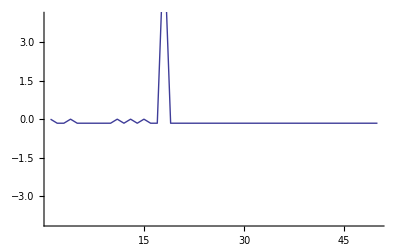
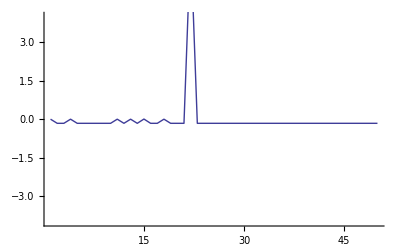
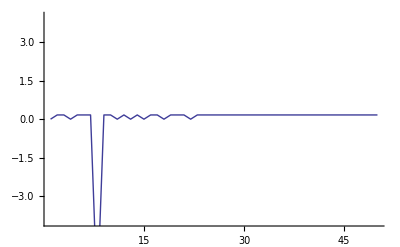

```mathematica
Table[ListPlot[ic[[i]],Joined->True,PlotRange->{-4,4}],{i,20}]
```

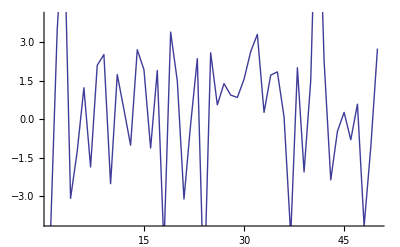
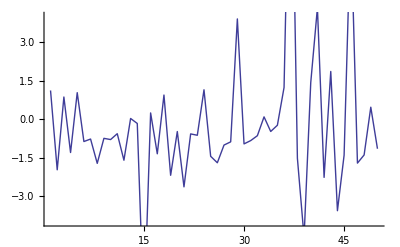
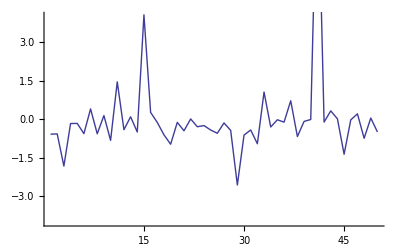
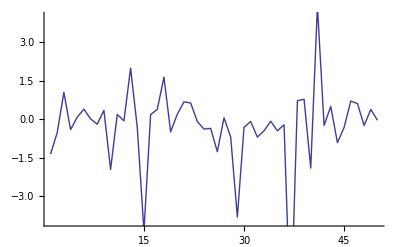
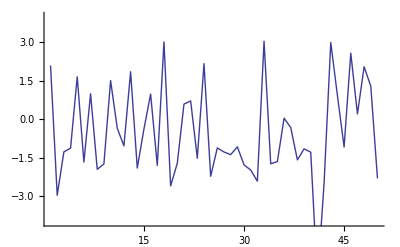
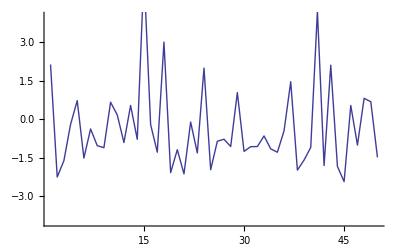
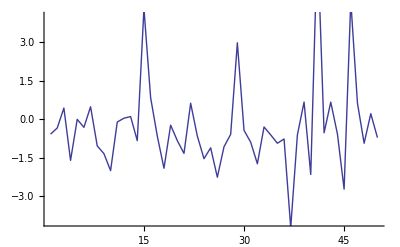
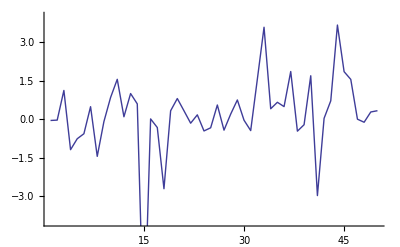

```mathematica
Table[ListPlot[ic2[[i]],Joined->True,PlotRange->{-4,4}],{i,20}]
```

## use one measure

```mathematica
p=mPCA[Flatten[data,{{1,2},{3,4}}]][[3]];
tp=p[[All,;;99]];
pd=Partition[tp,2];
Dimensions[pd]
```

{50,2,99}

```mathematica
pd1=pd[[All,1]];
```

```mathematica
Names["W`ICA`*"]
```

{fastICA}

```mathematica
{ic1,W,A}=fastICA[pd1ᵀ];(* usually num of sample should be bigger than that of feature*)
```

use default deltaW:1/1000, Maxstep:100

Dimension adjusted to 49 according to covariance matrix

Smallest remaining (non-zero) eigenvalue 0.000728528

Largest remaining (non-zero) eigenvalue 243.199

Sum of removed eigenvalues(Choped) 0

100.% of (non-zero) eigenvalues retained

whiten OK

guess OK

IC 1 computed in 9 steps

total time:0.984375seconds

```mathematica
Dimensions[W]
```

{49,99}

```mathematica
(*W.pd1ᵀ==ic1*)
Total[Chop[Correlation[ic1ᵀ]]];A.ic1-pd1ᵀ;
```

True

```mathematica
tic=ic1ᵀ;
```

```mathematica
Dimensions[tic]
Table[ListPlot[tic[[i]],Joined->True,PlotRange->{-1,1}],{i,10}]
```

{50,49}

```mathematica
(* we found W from one measure,will it work for another??*)
pd2=pd[[All,2]];
```

```mathematica
tic2=pd2.Wᵀ;
Dimensions[tic2]
```

```mathematica
Chop[Covariance[tic2]]
```

{{8.23217,0.810224,-12.698,0.372105,-4.80442,-6.59983,-10.3088,5.29561,2.02564,-3.53578,-2.0224,-4.72448,-2.1944,-8.84905,-6.5719,6.15824,-10.4042,2.67136,8.82157,-1.19175,8.82038,0.00480229,-0.650589,2.72842,2.20101,-1.28848,0.656107,4.16639,2.1226,4.46966,-5.97845,-4.25533,-2.74193,-3.06868,-2.20553,7.44142,-5.61317,3.94299,-8.29917,-0.723055,-6.50867,-3.82083,0.205535,3.33994,-4.27624,-2.78223,2.26206,9.25517,-1.41587},{0.810224,0.205543,-1.33415,-0.537352,0.447006,-0.374832,-0.980644,0.349236,0.407329,-1.13857,-0.552921,-0.289671,-0.151624,-0.344424,-0.826313,1.98796,-0.847855,0.104044,1.13494,-0.394957,0.6512,0.0202009,0.302116,0.389271,-0.184564,0.0110837,-1.21832,0.432189,-0.0533218,0.38891,-0.650863,-1.09016,0.333387,0.582224,0.527204,0.308319,-1.7839,0.397169,-0.182518,-0.193009,-0.205849,0.098506,-0.823774,-0.0790837,-0.642559,-0.625282,0.794584,-0.35816,-0.660777},{-12.698,-1.33415,48.8789,-12.2222,9.60412,20.1778,49.4781,-19.7684,-15.4204,2.71739,21.0926,9.43212,8.4066,43.9301,11.4457,-8.28111,39.9663,-14.3361,-21.5421,3.73632,-25.1534,4.65024,4.60482,-7.75545,-2.54486,1.61386,-6.64226,-2.31686,-4.34599,-10.9637,12.4316,40.9722,2.83538,2.1783,4.11277,-23.1423,8.49948,-10.9991,12.2499,3.52545,13.2086,8.15477,-14.6142,-23.5171,10.8893,11.5641,-14.0091,-34.9937,9.07947},{0.372105,-0.537352,-12.2222,13.4109,-6.75923,-6.85545,-13.0896,6.72831,3.89075,9.60121,-2.73943,-1.4492,-2.24497,-18.8224,4.84851,-14.9753,-11.6146,5.40009,-4.816,0.526016,4.39177,-3.08337,-3.59182,2.80229,0.479914,3.27248,9.19503,-0.990516,1.9949,2.52786,-0.126543,-17.8319,-5.58449,-4.2669,-5.44017,7.06728,9.40269,3.53189,-0.417886,-1.06444,-5.05753,-3.94686,10.002,11.3169,-1.72881,-3.38209,-0.0254365,16.8035,0.716534},{-4.80442,0.447006,9.60412,-6.75923,13.0293,8.45211,8.73258,-5.1932,0.338276,-7.72475,-1.7525,4.13221,1.85623,12.3182,0.51336,10.9224,11.0142,-5.4018,-3.48291,-1.9765,-8.43994,-0.560858,4.90888,-0.161683,-4.12325,1.45009,-12.8392,-1.36428,-2.88754,-4.62758,2.67263,-0.180364,6.58077,9.12991,8.20093,-7.77915,-8.95097,-2.495,8.6701,-0.0367449,8.73603,6.40307,-8.45856,-6.53716,-0.274527,0.274809,3.84882,-20.1394,-3.93305},{-6.59983,-0.374832,20.1778,-6.85545,8.45211,17.2493,22.9097,-10.0607,-6.06893,-3.61483,7.25633,4.10742,2.14122,21.7959,3.31558,-0.20253,20.3283,-7.89586,-6.94553,0.862139,-12.5419,1.40355,5.10887,0.024884,-0.438704,0.699169,-8.90089,0.179996,-3.29895,-4.78145,4.71245,15.2876,1.75188,1.08015,4.51435,-11.6444,-2.44845,-3.75606,6.57547,1.61716,6.44807,5.37506,-10.1141,-11.4389,3.61614,6.94708,-3.00261,-25.6607,3.54613},{-10.3088,-0.980644,49.4781,-13.0896,8.73258,22.9097,57.7505,-20.9794,-18.4677,2.42935,26.7167,8.36456,8.65716,48.4744,11.3127,-8.94817,41.0111,-14.5752,-20.6667,3.93587,-25.4959,6.80918,5.65861,-6.52081,-1.76751,1.83078,-7.70074,1.21594,-4.79579,-8.95746,11.3906,46.5294,-0.512707,-0.68007,3.00425,-23.6518,5.60684,-10.0171,10.5581,3.55609,9.51949,8.29037,-20.5031,-26.1091,10.2476,12.4358,-16.3835,-38.5536,10.666},{5.29561,0.349236,-19.7684,6.72831,-5.1932,-10.0607,-20.9794,9.47701,6.20152,1.98329,-7.92683,-3.67656,-2.68329,-20.1363,-3.18189,0.920647,-17.3832,6.4719,6.61282,-1.36929,10.3798,-2.03167,-2.95167,2.63123,0.712923,0.11238,5.00789,0.645047,2.43117,4.3433,-4.34317,-17.9664,-1.89509,-1.12493,-3.07819,10.6595,-0.94419,4.74549,-5.34294,-1.46199,-5.11549,-3.72745,7.58174,11.3446,-4.43934,-5.29631,4.93977,18.261,-3.41867},{2.02564,0.407329,-15.4204,3.89075,0.338276,-6.06893,-18.4677,6.20152,7.39466,-2.05701,-10.0667,-1.96729,-2.75595,-14.8439,-2.85999,4.43753,-11.6331,4.41182,6.12958,-1.82178,6.61818,-2.67409,-1.0701,1.85284,-0.511063,-0.00387708,0.341848,-1.2324,0.703487,1.91478,-3.26734,-17.5741,1.63985,2.23977,0.740827,6.1087,-3.55312,2.88838,-0.884168,-1.41284,-1.41428,-1.31072,5.28592,8.08478,-3.82851,-4.10746,7.04159,8.98414,-4.8289},{-3.53578,-1.13857,2.71739,9.60121,-7.72475,-3.61483,2.42935,1.98329,-2.05701,31.1564,7.87655,2.57297,4.38419,-7.54185,20.2643,-24.9944,-1.00256,8.11883,-10.559,3.05425,-2.89556,3.4599,-8.10469,-4.73969,-1.15932,5.30628,17.9569,-6.20432,-2.60376,1.27863,4.77471,-4.13712,-4.39655,-5.22374,-8.43283,-2.63692,16.9974,-1.83625,4.00438,-0.532795,-1.62763,0.0621465,5.68573,6.12982,5.41594,1.90807,-5.7684,18.1936,6.33196},{-2.0224,-0.552921,21.0926,-2.73943,-1.7525,7.25633,26.7167,-7.92683,-10.0667,7.87655,17.5207,2.49944,4.41105,18.4402,8.49487,-11.6199,16.2498,-4.78025,-11.6942,2.71134,-9.98446,3.65086,0.336959,-2.19169,0.503373,2.34709,1.7648,2.03188,-1.34638,-1.90915,4.67274,21.5765,-4.56874,-4.77924,-2.80817,-8.61011,6.2756,-3.21174,1.82206,1.66326,-0.390855,1.38883,-8.37727,-10.208,4.69473,5.32846,-10.5866,-10.502,7.52171},{-4.72448,-0.289671,9.43212,-1.4492,4.13221,4.10742,8.36456,-3.67656,-1.96729,2.57297,2.49944,4.3952,2.568,7.14659,5.13722,-2.52349,7.48531,-2.52452,-7.18078,0.314408,-6.81349,0.328921,1.07223,-1.1845,-2.52988,2.31567,-2.65419,-2.33502,-1.63666,-3.1593,4.3903,1.61801,2.35394,3.53755,2.5958,-5.98376,1.63298,-2.26594,6.47092,0.279186,4.88601,3.30292,-2.40278,-3.1822,2.48928,0.644248,-1.43976,-7.77671,0.732342},{-2.1944,-0.151624,8.4066,-2.24497,1.85623,2.14122,8.65716,-2.68329,-2.75595,4.38419,4.41105,2.568,3.19138,7.01889,4.62569,-1.53597,5.73335,-1.08295,-4.76743,0.444722,-4.64004,1.97667,-0.330391,-2.4955,-1.8849,1.33825,-0.0922702,-1.21495,-1.36771,-1.65459,2.80368,5.56788,1.38615,2.00919,0.509977,-4.40036,1.44815,-2.26179,3.41081,0.21848,3.18513,2.3459,-3.26656,-3.29299,2.16678,0.926915,-2.46512,-3.35712,0.991792},{-8.84905,-0.344424,43.9301,-18.8224,12.3182,21.7959,48.4744,-20.1363,-14.8439,-7.54185,18.4402,7.14659,7.01889,49.2945,2.6105,5.89935,37.3854,-14.1453,-9.78941,2.38932,-20.9191,7.038,6.87238,-7.62328,-1.9245,-2.53729,-12.3582,0.0678394,-5.35355,-8.58472,8.38748,45.4097,5.68602,3.66662,6.93346,-22.1427,-2.44183,-10.5372,8.96251,3.08315,12.2679,8.64573,-20.1165,-26.7095,9.0632,11.6439,-10.8663,-40.1721,5.92678},{-6.5719,-0.826313,11.4457,4.84851,0.51336,3.31558,11.3127,-3.18189,-2.85999,20.2643,8.49487,5.13722,4.62569,2.6105,21.0113,-20.3311,9.55694,0.626548,-17.2427,1.83049,-10.663,0.701376,-2.76016,-1.57652,-3.28978,7.91348,5.43156,-4.66482,-3.58856,-2.9462,7.22994,-4.053,-2.30436,0.315235,-1.70001,-8.54971,10.9372,-2.47509,10.8029,0.029521,2.61405,3.7551,-1.32682,-0.391998,4.81861,2.13337,-4.33968,-1.40699,5.23514},{6.15824,1.98796,-8.28111,-14.9753,10.9224,-0.20253,-8.94817,0.920647,4.43753,-24.9944,-11.6199,-2.52349,-1.53597,5.89935,-20.3311,40.398,-5.12084,-1.92039,21.3225,-4.95309,6.9227,1.4762,5.40421,-0.619642,-1.20528,-7.53352,-17.1613,3.19345,0.0845365,1.04353,-7.87166,2.40786,11.4423,11.0055,9.90917,2.52053,-24.7221,0.474613,-5.18132,-0.977893,4.45858,3.12556,-8.88078,-5.12038,-6.29388,-4.09714,10.8032,-10.7513,-11.2865},{-10.4042,-0.847855,39.9663,-11.6146,11.0142,20.3283,41.0111,-17.3832,-11.6331,-1.00256,16.2498,7.48531,5.73335,37.3854,9.55694,-5.12084,37.4955,-14.1372,-17.814,2.41884,-22.3207,2.24601,6.13123,-3.28836,-1.85014,3.02896,-10.2076,-0.798977,-4.48866,-9.5301,9.50702,31.7024,1.83139,1.99242,5.86448,-20.8367,2.23372,-7.87657,11.1953,2.9557,11.0635,7.66876,-15.0084,-21.1612,7.94452,10.9211,-8.8335,-37.3682,7.44831},{2.67136,0.104044,-14.3361,5.40009,-5.4018,-7.89586,-14.5752,6.4719,4.41182,8.11883,-4.78025,-2.52452,-1.08295,-14.1453,0.626548,-1.92039,-14.1372,9.68807,8.7448,0.00421166,8.46218,1.98815,-5.13914,-3.15625,0.667534,-2.1579,10.1603,-2.88307,-0.10207,4.38926,-2.95511,-9.54218,-0.0453358,-1.98654,-4.5689,6.08182,2.82938,1.37976,-3.03306,-1.57761,-4.08908,-2.05461,6.42008,8.85115,-1.18065,-2.54862,2.55266,19.5228,-1.98198},{8.82157,1.13494,-21.5421,-4.816,-3.48291,-6.94553,-20.6667,6.61282,6.12958,-10.559,-11.6942,-7.18078,-4.76743,-9.78941,-17.2427,21.3225,-17.814,8.7448,30.2346,-1.66052,16.8587,3.92091,-2.13664,-3.77566,4.27404,-10.8572,3.6468,0.285255,0.740518,6.74794,-10.1691,0.733532,4.13364,-2.00993,-1.20321,9.92254,-11.1783,1.83744,-12.7361,-1.48176,-5.55331,-3.17988,2.84428,4.7117,-4.32391,-1.06144,8.06398,14.6856,-6.00967},{-1.19175,-0.394957,3.73632,0.526016,-1.9765,0.862139,3.93587,-1.36929,-1.82178,3.05425,2.71134,0.314408,0.444722,2.38932,1.83049,-4.95309,2.41884,0.00421166,-1.66052,1.22975,-1.18753,0.862881,-0.926117,-1.43448,0.788095,-0.522492,3.49053,-0.72995,-0.154627,-0.32237,1.25504,5.32352,-1.19914,-2.27543,-1.75936,-1.1756,4.25235,-1.1608,-0.206635,0.471199,-0.323627,-0.451342,1.03401,-0.956474,1.97811,1.96262,-2.76413,0.977489,2.28369},{8.82038,0.6512,-25.1534,4.39177,-8.43994,-12.5419,-25.4959,10.3798,6.61818,-2.89556,-9.98446,-6.81349,-4.64004,-20.9191,-10.663,6.9227,-22.3207,8.46218,16.8587,-1.18753,16.6076,-0.331178,-3.6877,1.28079,3.14683,-4.61146,7.22373,1.62602,3.09212,6.99698,-8.18453,-12.0726,-1.48906,-3.83481,-4.37851,13.9583,-3.26209,4.77972,-11.5085,-1.50484,-8.252,-6.27754,8.79212,10.9962,-4.80906,-4.68438,5.31446,23.1609,-4.02679},{0.00480229,0.0202009,4.65024,-3.08337,-0.560858,1.40355,6.80918,-2.03167,-2.67409,3.4599,3.65086,0.328921,1.97667,7.038,0.701376,1.4762,2.24601,1.98815,3.92091,0.862881,-0.331178,5.24782,-1.64887,-5.0773,-0.135241,-2.48737,3.78489,-1.68853,-1.75709,0.822405,0.220731,10.9223,1.61436,-0.813062,-1.2107,-2.53005,0.984023,-2.73402,-0.232374,-0.187998,0.76975,1.13885,-2.95485,-3.33414,2.29018,2.49282,-2.55197,1.6641,0.817123},{-0.650589,0.302116,4.60482,-3.59182,4.90888,5.10887,5.65861,-2.95167,-1.0701,-8.10469,0.336959,1.07223,-0.330391,6.87238,-2.76016,5.40421,6.13123,-5.13914,-2.13664,-0.926117,-3.6877,-1.64887,4.23351,3.13968,-0.537802,0.966211,-8.9988,2.55641,-0.0696394,-1.88511,0.454349,1.51051,0.791754,2.31344,4.03049,-2.82864,-5.76694,0.372533,1.89755,0.493805,2.07791,1.5916,-4.96359,-4.46134,-1.08332,0.261747,0.931366,-13.2231,-0.512998},{2.72842,0.389271,-7.75545,2.80229,-0.161683,0.024884,-6.52081,2.63123,1.85284,-4.73969,-2.19169,-1.1845,-2.4955,-7.62328,-1.57652,-0.619642,-3.28836,-3.15625,-3.77566,-1.43448,1.28079,-5.0773,3.13968,9.88939,0.44193,4.8481,-7.34278,5.06209,1.92758,1.12463,-1.72586,-13.5111,-3.94247,-0.660294,1.87018,3.72513,-5.47195,5.16301,-1.23639,0.0912999,-3.60747,-1.96722,-0.276878,2.85376,-3.78788,-3.14734,2.77632,-4.80918,-0.166047},{2.20101,-0.184564,-2.54486,0.479914,-4.12325,-0.438704,-1.76751,0.712923,-0.511063,-1.15932,0.503373,-2.52988,-1.8849,-1.9245,-3.28978,-1.20528,-1.85014,0.667534,4.27404,0.788095,3.14683,-0.135241,-0.537802,0.44193,3.65948,-2.55756,3.29537,1.50861,1.41357,1.38316,-2.29078,4.43236,-2.65614,-4.99745,-2.71532,2.6541,1.32809,0.911994,-5.65564,0.600069,-3.97462,-2.57547,2.06273,0.669436,-0.394555,1.89551,-0.886278,3.40689,1.77908},{-1.28848,0.0110837,1.61386,3.27248,1.45009,0.699169,1.83078,0.11238,-0.00387708,5.30628,2.34709,2.31567,1.33825,-2.53729,7.91348,-7.53352,3.02896,-2.1579,-10.8572,-0.522492,-4.61146,-2.48737,0.966211,4.8481,-2.55756,8.25839,-3.85588,0.844924,-0.439989,-0.754147,2.4876,-10.2092,-2.07019,1.63809,1.77517,-2.27849,0.195366,1.91904,5.51359,-0.275783,0.42817,1.04457,-2.10027,0.732747,-0.464464,-1.83158,0.137949,-4.44412,0.973902},{0.656107,-1.21832,-6.64226,9.19503,-12.8392,-8.90089,-7.70074,5.00789,0.341848,17.9569,1.7648,-2.65419,-0.0922702,-12.3582,5.43156,-17.1613,-10.2076,10.1603,3.6468,3.49053,7.22373,3.78489,-8.9988,-7.34278,3.29537,-3.85588,24.3627,-5.16385,0.729871,3.82825,-0.21885,4.30212,-4.91737,-9.45745,-11.3192,6.33365,17.1686,-1.52794,-6.5532,-0.418645,-5.91754,-5.1802,12.6811,9.10504,3.56683,2.82741,-5.50069,28.8477,4.18229},{4.16639,0.432189,-2.31686,-0.990516,-1.36428,0.179996,1.21594,0.645047,-1.2324,-6.20432,2.03188,-2.33502,-1.21495,0.0678394,-4.66482,3.19345,-0.798977,-2.88307,0.285255,-0.72995,1.62602,-1.68853,2.55641,5.06209,1.50861,0.844924,-5.16385,6.23758,2.04206,1.42968,-2.51138,0.667807,-3.62664,-2.21157,-0.0589468,2.67408,-5.1196,3.02187,-4.22388,0.444772,-3.85002,-2.07126,-3.2633,-1.32934,-3.02469,-1.10919,-0.365378,-4.1363,0.588682},{2.1226,-0.0533218,-4.34599,1.9949,-2.88754,-3.29895,-4.79579,2.43117,0.703487,-2.60376,-1.34638,-1.63666,-1.36771,-5.35355,-3.58856,0.0845365,-4.48866,-0.10207,0.740518,-0.154627,3.09212,-1.75709,-0.0696394,1.92758,1.41357,-0.439989,0.729871,2.04206,2.52422,0.780078,-1.41624,-2.34764,-2.03529,-1.68051,-1.40021,4.32416,0.663605,1.86321,-3.61256,0.195222,-2.49078,-2.35264,2.96138,2.68438,-1.88064,-1.56574,0.00342588,4.37562,-0.216323},{4.46966,0.38891,-10.9637,2.52786,-4.62758,-4.78145,-8.95746,4.3433,1.91478,1.27863,-1.90915,-3.1593,-1.65459,-8.58472,-2.9462,1.04353,-9.5301,4.38926,6.74794,-0.32237,6.99698,0.822405,-1.88511,1.12463,1.38316,-0.754147,3.82825,1.42968,0.780078,4.66748,-3.7967,-4.49708,-1.87318,-2.78143,-2.54073,5.54745,-1.4076,2.56241,-5.05675,-0.899554,-5.04924,-2.88805,2.23042,4.24357,-1.9526,-1.70127,1.22979,10.1638,-0.843685},{-5.97845,-0.650863,12.4316,-0.126543,2.67263,4.71245,11.3906,-4.34317,-3.26734,4.77471,4.67274,4.3903,2.80368,8.38748,7.22994,-7.87166,9.50702,-2.95511,-10.1691,1.25504,-8.18453,0.220731,0.454349,-1.72586,-2.29078,2.4876,-0.21885,-2.51138,-1.41624,-3.7967,6.33108,4.1909,0.582425,2.17138,1.04804,-6.24666,5.7344,-2.8753,7.24461,0.684214,4.82017,3.05963,-1.2149,-3.20109,3.64455,1.71932,-3.64414,-7.44902,2.61356},{-4.25533,-1.09016,40.9722,-17.8319,-0.180364,15.2876,46.5294,-17.9664,-17.5741,-4.13712,21.5765,1.61801,5.56788,45.4097,-4.053,2.40786,31.7024,-9.54218,0.733532,5.32352,-12.0726,10.9223,1.51051,-13.5111,4.43236,-10.2092,4.30212,0.667807,-2.34764,-4.49708,4.1909,67.2098,0.965948,-6.92338,-2.32184,-15.2825,6.62635,-11.8237,-4.58926,3.87184,5.00522,2.47132,-13.0744,-24.7592,11.1153,16.0041,-17.0552,-21.0071,9.73722},{-2.74193,0.333387,2.83538,-5.58449,6.58077,1.75188,-0.512707,-1.89509,1.63985,-4.39655,-4.56874,2.35394,1.38615,5.68602,-2.30436,11.4423,1.83139,-0.0453358,4.13364,-1.19914,-1.48906,1.61436,0.791754,-3.94247,-2.65614,-2.07019,-4.91737,-3.62664,-2.03529,-1.87318,0.582425,0.965948,8.63886,7.15053,4.93767,-3.47315,-5.0786,-2.95251,4.00277,-0.454241,6.61494,3.83653,-2.20754,-2.73083,1.00606,-0.683654,3.65817,-5.14127,-4.51405},{-3.06868,0.582224,2.1783,-4.2669,9.12991,1.08015,-0.68007,-1.12493,2.23977,-5.22374,-4.77924,3.53755,2.00919,3.66662,0.315235,11.0055,1.99242,-1.98654,-2.00993,-2.27543,-3.83481,-0.813062,2.31344,-0.660294,-4.99745,1.63809,-9.45745,-2.21157,-1.68051,-2.78143,2.17138,-6.92338,7.15053,10.926,6.95556,-3.67895,-6.99778,-1.4006,7.81388,-0.82785,7.64715,5.11896,-3.69026,-1.68061,-0.748077,-3.70401,4.63308,-8.68019,-5.48519},{-2.20553,0.527204,4.11277,-5.44017,8.20093,4.51435,3.00425,-3.07819,0.740827,-8.43283,-2.80817,2.5958,0.509977,6.93346,-1.70001,9.90917,5.86448,-4.5689,-1.20321,-1.75936,-4.37851,-1.2107,4.03049,1.87018,-2.71532,1.77517,-11.3192,-0.0589468,-1.40021,-2.54073,1.04804,-2.32184,4.93767,6.95556,7.27383,-4.59259,-8.27934,-0.579474,5.20427,-0.0618167,5.08155,3.82545,-5.69468,-4.65818,-0.614632,-0.924338,3.68496,-14.4455,-3.14395},{7.44142,0.308319,-23.1423,7.06728,-7.77915,-11.6444,-23.6518,10.6595,6.1087,-2.63692,-8.61011,-5.98376,-4.40036,-22.1427,-8.54971,2.52053,-20.8367,6.08182,9.92254,-1.1756,13.9583,-2.53005,-2.82864,3.72513,2.6541,-2.27849,6.33365,2.67408,4.32416,5.54745,-6.24666,-15.2825,-3.47315,-3.67895,-4.59259,15.2842,-1.13189,5.48371,-10.2788,-1.04727,-7.57583,-6.21261,9.93564,12.4261,-5.41327,-5.31683,4.23336,21.1159,-3.63413},{-5.61317,-1.7839,8.49948,9.40269,-8.95097,-2.44845,5.60684,-0.94419,-3.55312,16.9974,6.2756,1.63298,1.44815,-2.44183,10.9372,-24.7221,2.23372,2.82938,-11.1783,4.25235,-3.26209,0.984023,-5.76694,-5.47195,1.32809,0.195366,17.1686,-5.1196,0.663605,-1.4076,5.7344,6.62635,-5.0786,-6.99778,-8.27934,-1.13189,22.6127,-3.36919,1.83068,0.824893,-0.676272,-2.63148,10.6093,3.28986,6.15661,3.80852,-9.37108,14.2897,7.4494},{3.94299,0.397169,-10.9991,3.53189,-2.495,-3.75606,-10.0171,4.74549,2.88838,-1.83625,-3.21174,-2.26594,-2.26179,-10.5372,-2.47509,0.474613,-7.87657,1.37976,1.83744,-1.1608,4.77972,-2.73402,0.372533,5.16301,0.911994,1.91904,-1.52794,3.02187,1.86321,2.56241,-2.8753,-11.8237,-2.95251,-1.4006,-0.579474,5.48371,-3.36919,4.79938,-3.31849,-0.525351,-4.36986,-2.27121,1.9077,5.1114,-3.69865,-3.33999,2.98321,4.57048,-1.02887},{-8.29917,-0.182518,12.2499,-0.417886,8.6701,6.57547,10.5581,-5.34294,-0.884168,4.00438,1.82206,6.47092,3.41081,8.96251,10.8029,-5.18132,11.1953,-3.03306,-12.7361,-0.206635,-11.5085,-0.232374,1.89755,-1.23639,-5.65564,5.51359,-6.5532,-4.22388,-3.61256,-5.05675,7.24461,-4.58926,4.00277,7.81388,5.20427,-10.2788,1.83068,-3.31849,15.6842,-0.478201,8.28985,6.39901,-4.63731,-3.87209,2.50276,-0.185722,0.0400711,-13.8759,-0.257389},{-0.723055,-0.193009,3.52545,-1.06444,-0.0367449,1.61716,3.55609,-1.46199,-1.41284,-0.532795,1.66326,0.279186,0.21848,3.08315,0.029521,-0.977893,2.9557,-1.57761,-1.48176,0.471199,-1.50484,-0.187998,0.493805,0.0912999,0.600069,-0.275783,-0.418645,0.444772,0.195222,-0.899554,0.684214,3.87184,-0.454241,-0.82785,-0.0618167,-1.04727,0.824893,-0.525351,-0.478201,0.655852,0.32075,0.0554774,-0.44018,-1.69197,0.904707,1.21599,-1.34112,-2.73212,1.16065},{-6.50867,-0.205849,13.2086,-5.05753,8.73603,6.44807,9.51949,-5.11549,-1.41428,-1.62763,-0.390855,4.88601,3.18513,12.2679,2.61405,4.45858,11.0635,-4.08908,-5.55331,-0.323627,-8.252,0.76975,2.07791,-3.60747,-3.97462,0.42817,-5.91754,-3.85002,-2.49078,-5.04924,4.82017,5.00522,6.61494,7.64715,5.08155,-7.57583,-0.676272,-4.36986,8.28985,0.32075,10.9474,5.50704,-2.93042,-5.69083,3.19976,1.43439,0.351635,-12.4163,-1.58183},{-3.82083,0.098506,8.15477,-3.94686,6.40307,5.37506,8.29037,-3.72745,-1.31072,0.0621465,1.38883,3.30292,2.3459,8.64573,3.7551,3.12556,7.66876,-2.05461,-3.17988,-0.451342,-6.27754,1.13885,1.5916,-1.96722,-2.57547,1.04457,-5.1802,-2.07126,-2.35264,-2.88805,3.05963,2.47132,3.83653,5.11896,3.82545,-6.21261,-2.63148,-2.27121,6.39901,0.0554774,5.50704,5.04555,-5.17138,-4.22364,1.50207,0.777472,0.815978,-10.3958,-0.935462},{0.205535,-0.823774,-14.6142,10.002,-8.45856,-10.1141,-20.5031,7.58174,5.28592,5.68573,-8.37727,-2.40278,-3.26656,-20.1165,-1.32682,-8.88078,-15.0084,6.42008,2.84428,1.03401,8.79212,-2.95485,-4.96359,-0.276878,2.06273,-2.10027,12.6811,-3.2633,2.96138,2.23042,-1.2149,-13.0744,-2.20754,-3.69026,-5.69468,9.93564,10.6093,1.9077,-4.63731,-0.44018,-2.93042,-5.17138,17.0758,12.3554,-0.0595246,-2.38794,1.16769,22.7994,-0.312162},{3.33994,-0.0790837,-23.5171,11.3169,-6.53716,-11.4389,-26.1091,11.3446,8.08478,6.12982,-10.208,-3.1822,-3.29299,-26.7095,-0.391998,-5.12038,-21.1612,8.85115,4.7117,-0.956474,10.9962,-3.33414,-4.46134,2.85376,0.669436,0.732747,9.10504,-1.32934,2.68438,4.24357,-3.20109,-24.7592,-2.73083,-1.68061,-4.65818,12.4261,3.28986,5.1114,-3.87209,-1.69197,-5.69083,-4.22364,12.3554,16.3936,-4.2934,-6.12236,5.30015,23.7841,-3.41083},{-4.27624,-0.642559,10.8893,-1.72881,-0.274527,3.61614,10.2476,-4.43934,-3.82851,5.41594,4.69473,2.48928,2.16678,9.0632,4.81861,-6.29388,7.94452,-1.18065,-4.32391,1.97811,-4.80906,2.29018,-1.08332,-3.78788,-0.394555,-0.464464,3.56683,-3.02469,-1.88064,-1.9526,3.64455,11.1153,1.00606,-0.748077,-0.614632,-5.41327,6.15661,-3.69865,2.50276,0.904707,3.19976,1.50207,-0.0595246,-4.2934,5.52806,3.7679,-4.56733,-2.75052,3.16441},{-2.78223,-0.625282,11.5641,-3.38209,0.274809,6.94708,12.4358,-5.29631,-4.10746,1.90807,5.32846,0.644248,0.926915,11.6439,2.13337,-4.09714,10.9211,-2.54862,-1.06144,1.96262,-4.68438,2.49282,0.261747,-3.14734,1.89551,-1.83158,2.82741,-1.10919,-1.56574,-1.70127,1.71932,16.0041,-0.683654,-3.70401,-0.924338,-5.31683,3.80852,-3.33999,-0.185722,1.21599,1.43439,0.777472,-2.38794,-6.12236,3.7679,7.11099,-3.97249,-6.89018,4.15237},{2.26206,0.794584,-14.0091,-0.0254365,3.84882,-3.00261,-16.3835,4.93977,7.04159,-5.7684,-10.5866,-1.43976,-2.46512,-10.8663,-4.33968,10.8032,-8.8335,2.55266,8.06398,-2.76413,5.31446,-2.55197,0.931366,2.77632,-0.886278,0.137949,-5.50069,-0.365378,0.00342588,1.22979,-3.64414,-17.0552,3.65817,4.63308,3.68496,4.23336,-9.37108,2.98321,0.0400711,-1.34112,0.351635,0.815978,1.16769,5.30015,-4.56733,-3.97249,9.48079,1.51087,-5.9634},{9.25517,-0.35816,-34.9937,16.8035,-20.1394,-25.6607,-38.5536,18.261,8.98414,18.1936,-10.502,-7.77671,-3.35712,-40.1721,-1.40699,-10.7513,-37.3682,19.5228,14.6856,0.977489,23.1609,1.6641,-13.2231,-4.80918,3.40689,-4.44412,28.8477,-4.1363,4.37562,10.1638,-7.44902,-21.0071,-5.14127,-8.68019,-14.4455,21.1159,14.2897,4.57048,-13.8759,-2.73212,-12.4163,-10.3958,22.7994,23.7841,-2.75052,-6.89018,1.51087,56.6543,-2.19065},{-1.41587,-0.660777,9.07947,0.716534,-3.93305,3.54613,10.666,-3.41867,-4.8289,6.33196,7.52171,0.732342,0.991792,5.92678,5.23514,-11.2865,7.44831,-1.98198,-6.00967,2.28369,-4.02679,0.817123,-0.512998,-0.166047,1.77908,0.973902,4.18229,0.588682,-0.216323,-0.843685,2.61356,9.73722,-4.51405,-5.48519,-3.14395,-3.63413,7.4494,-1.02887,-0.257389,1.16065,-1.58183,-0.935462,-0.312162,-3.41083,3.16441,4.15237,-5.9634,-2.19065,6.65446}}

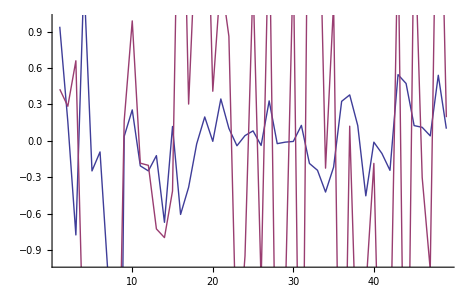
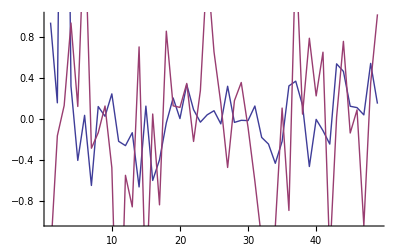
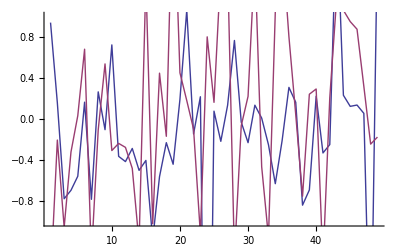
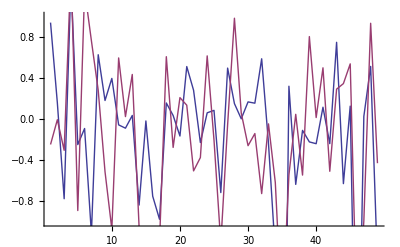
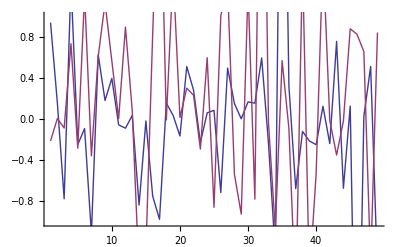
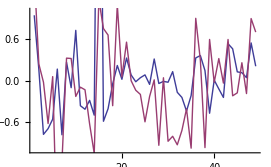
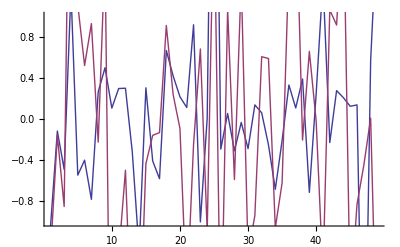
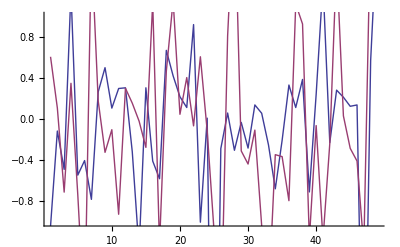

```mathematica
Table[ListPlot[{tic[[i]],tic2[[i]]},Joined->True,PlotRange->{-1,1}],{i,10}]
```

```mathematica
samp={tic,tic2}ᵀ;
Dimensions[samp]
```

{50,2,49}

```mathematica
{dd,ds}=eucDist[samp];
```

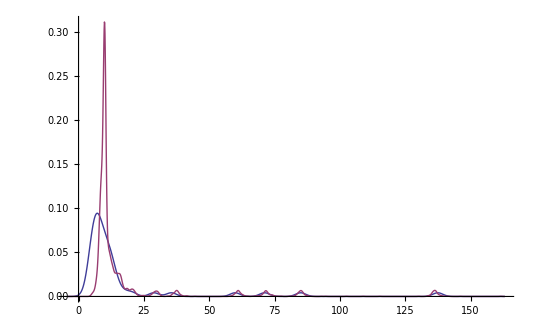

```mathematica
SmoothHistogram[{ds,dd}]
(* it seems not very well*)
```

```mathematica
TTest[{dd,ds},0,"TestConclusion"]
```

TTest::nortst: At least one of the p-values in {0., 0.}, resulting from a test for normality, is below 0.025. The tests in {"T"} require that the data is normally distributed.

Intersection::normal: Nonatomic expression expected at position 2 in {"PairedT", "T", "Z", "KSampleT"} ∩ "T".

TTest::nortst: At least one of the p-values in {0., 0.}, resulting from a test for normality, is below 0.025. The tests in {"PairedT", "T", "Z", "KSampleT"} ∩ "T" require that the data is normally distributed.

The null hypothesis that the median difference is 0 is not rejected at the 5. percent level based on the T test.

```mathematica
(*test J1 of each ICA feature*)
sj1=Table[J1[samp[[;;,;;,i]]],{i,Length[samp[[1,1]]]}];
```

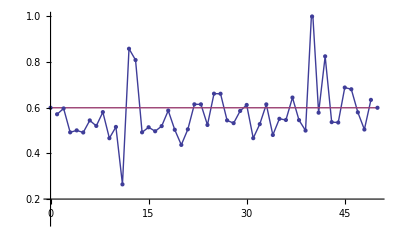

```mathematica
ListPlot[{sj1,{{0,0.6},{50,0.6}}},Joined->True,PlotRange->{0.1,1},Mesh->Full]
```

```mathematica
Export["..\\tmp\\pd.mat",pd1]
```

..\tmp\pd.mat